```mathematica
ExplainContractionCounts[g_,e_]:=Block[{
gBis=SortGraph[g], 
taken={e[[1]],e[[2]]},
comp=SortGraph[VertexDelete[VertexDelete[GraphComplement[g],e[[1]]],e[[2]]]],
nonEdges=0,
remainingNonEdges=0,
result},
result=Table[
If[!EdgeQ[gBis,e[[1]]<->v]&&!EdgeQ[gBis,e[[2]]<->v],
nonEdges++
]
,{v,Select[VertexList[gBis],!MemberQ[taken,#]&]}
];
remainingNonEdges=Length[EdgeList[comp]];
{nonEdges,remainingNonEdges}
]
```

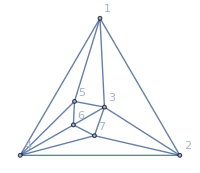
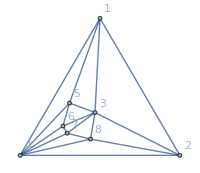
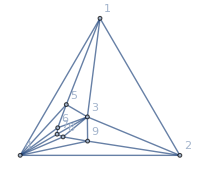
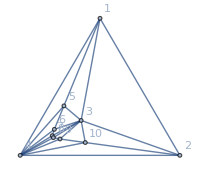
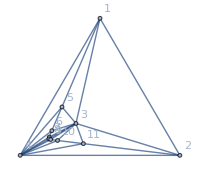
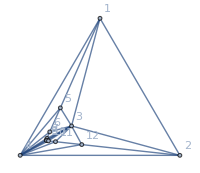
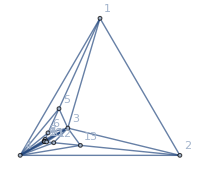
{-Graphics-7
{0,3}<->{1<->3,1}
{0,3}<->{1<->4,1}
{0,3}<->{2<->3,1}
{0,3}<->{2<->4,1}
{0,3}<->{3<->5,1}
{0,3}<->{3<->6,1}
{0,3}<->{3<->7,1}
{0,3}<->{4<->5,1}
{0,3}<->{4<->6,1}
{0,3}<->{4<->7,1}
{1,2}<->{1<->2,4}
{1,2}<->{1<->5,4}
{1,2}<->{2<->7,4}
{1,2}<->{5<->6,4}
{1,2}<->{6<->7,4},-Graphics-8
{0,6}<->{1<->3,1}
{0,6}<->{1<->4,1}
{0,6}<->{2<->3,1}
{0,6}<->{2<->4,1}
{0,6}<->{3<->5,1}
{0,6}<->{3<->6,1}
{0,6}<->{3<->7,1}
{0,6}<->{3<->8,1}
{0,6}<->{4<->5,1}
{0,6}<->{4<->6,1}
{0,6}<->{4<->7,1}
{0,6}<->{4<->8,1}
{2,4}<->{1<->2,5}
{2,4}<->{1<->5,5}
{2,4}<->{2<->8,5}
{2,4}<->{5<->6,5}
{2,4}<->{6<->7,5}
{2,4}<->{7<->8,5},-Graphics-9
{0,10}<->{1<->3,1}
{0,10}<->{1<->4,1}
{0,10}<->{2<->3,1}
{0,10}<->{2<->4,1}
{0,10}<->{3<->5,1}
{0,10}<->{3<->6,1}
{0,10}<->{3<->7,1}
{0,10}<->{3<->8,1}
{0,10}<->{3<->9,1}
{0,10}<->{4<->5,1}
{0,10}<->{4<->6,1}
{0,10}<->{4<->7,1}
{0,10}<->{4<->8,1}
{0,10}<->{4<->9,1}
{3,7}<->{1<->2,12}
{3,7}<->{1<->5,12}
{3,7}<->{2<->9,12}
{3,7}<->{5<->6,12}
{3,7}<->{6<->7,12}
{3,7}<->{7<->8,12}
{3,7}<->{8<->9,12},-Graphics-10
{0,15}<->{1<->3,1}
{0,15}<->{1<->4,1}
{0,15}<->{2<->3,1}
{0,15}<->{2<->4,1}
{0,15}<->{3<->5,1}
{0,15}<->{3<->6,1}
{0,15}<->{3<->7,1}
{0,15}<->{3<->8,1}
{0,15}<->{3<->9,1}
{0,15}<->{3<->10,1}
{0,15}<->{4<->5,1}
{0,15}<->{4<->6,1}
{0,15}<->{4<->7,1}
{0,15}<->{4<->8,1}
{0,15}<->{4<->9,1}
{0,15}<->{4<->10,1}
{4,11}<->{1<->2,21}
{4,11}<->{1<->5,21}
{4,11}<->{2<->10,21}
{4,11}<->{5<->6,21}
{4,11}<->{6<->7,21}
{4,11}<->{7<->8,21}
{4,11}<->{8<->9,21}
{4,11}<->{9<->10,21},-Graphics-11
{0,21}<->{1<->3,1}
{0,21}<->{1<->4,1}
{0,21}<->{2<->3,1}
{0,21}<->{2<->4,1}
{0,21}<->{3<->5,1}
{0,21}<->{3<->6,1}
{0,21}<->{3<->7,1}
{0,21}<->{3<->8,1}
{0,21}<->{3<->9,1}
{0,21}<->{3<->10,1}
{0,21}<->{3<->11,1}
{0,21}<->{4<->5,1}
{0,21}<->{4<->6,1}
{0,21}<->{4<->7,1}
{0,21}<->{4<->8,1}
{0,21}<->{4<->9,1}
{0,21}<->{4<->10,1}
{0,21}<->{4<->11,1}
{5,16}<->{1<->2,44}
{5,16}<->{1<->5,44}
{5,16}<->{2<->11,44}
{5,16}<->{5<->6,44}
{5,16}<->{6<->7,44}
{5,16}<->{7<->8,44}
{5,16}<->{8<->9,44}
{5,16}<->{9<->10,44}
{5,16}<->{10<->11,44},-Graphics-12
{0,28}<->{1<->3,1}
{0,28}<->{1<->4,1}
{0,28}<->{2<->3,1}
{0,28}<->{2<->4,1}
{0,28}<->{3<->5,1}
{0,28}<->{3<->6,1}
{0,28}<->{3<->7,1}
{0,28}<->{3<->8,1}
{0,28}<->{3<->9,1}
{0,28}<->{3<->10,1}
{0,28}<->{3<->11,1}
{0,28}<->{3<->12,1}
{0,28}<->{4<->5,1}
{0,28}<->{4<->6,1}
{0,28}<->{4<->7,1}
{0,28}<->{4<->8,1}
{0,28}<->{4<->9,1}
{0,28}<->{4<->10,1}
{0,28}<->{4<->11,1}
{0,28}<->{4<->12,1}
{6,22}<->{1<->2,85}
{6,22}<->{1<->5,85}
{6,22}<->{2<->12,85}
{6,22}<->{5<->6,85}
{6,22}<->{6<->7,85}
{6,22}<->{7<->8,85}
{6,22}<->{8<->9,85}
{6,22}<->{9<->10,85}
{6,22}<->{10<->11,85}
{6,22}<->{11<->12,85},-Graphics-13
{0,36}<->{1<->3,1}
{0,36}<->{1<->4,1}
{0,36}<->{2<->3,1}
{0,36}<->{2<->4,1}
{0,36}<->{3<->5,1}
{0,36}<->{3<->6,1}
{0,36}<->{3<->7,1}
{0,36}<->{3<->8,1}
{0,36}<->{3<->9,1}
{0,36}<->{3<->10,1}
{0,36}<->{3<->11,1}
{0,36}<->{3<->12,1}
{0,36}<->{3<->13,1}
{0,36}<->{4<->5,1}
{0,36}<->{4<->6,1}
{0,36}<->{4<->7,1}
{0,36}<->{4<->8,1}
{0,36}<->{4<->9,1}
{0,36}<->{4<->10,1}
{0,36}<->{4<->11,1}
{0,36}<->{4<->12,1}
{0,36}<->{4<->13,1}
{7,29}<->{1<->2,172}
{7,29}<->{1<->5,172}
{7,29}<->{2<->13,172}
{7,29}<->{5<->6,172}
{7,29}<->{6<->7,172}
{7,29}<->{7<->8,172}
{7,29}<->{8<->9,172}
{7,29}<->{9<->10,172}
{7,29}<->{10<->11,172}
{7,29}<->{11<->12,172}
{7,29}<->{12<->13,172}}

```mathematica
Table[
With[{g=SortGraph[JacobsThalGraph[k]]},
Column[{Labeled[Graph[g,VertexLabels->"Name", GraphLayout->"TutteEmbedding",GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick", ImageSize->200],Style[VertexCount[g],Red]],
TableForm[Sort[Table[
ExplainContractionCounts[g,e]<->{e,ChromaticPolynomial[EdgeContract[g,e],4]/24},{e,CollectMPGEdges[g]}
]]]}]]
,{k,3,9}]
```

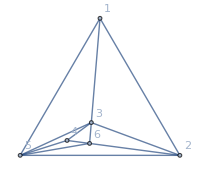
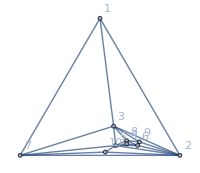
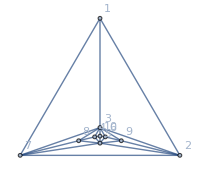
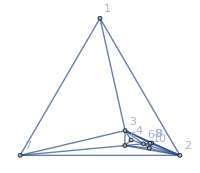
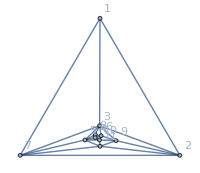
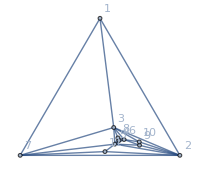
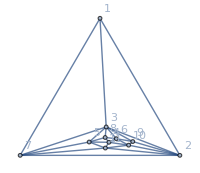
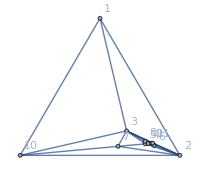
{-Graphics-6
{0,1}<->{1<->3,1}
{0,1}<->{1<->5,1}
{0,1}<->{2<->6,1}
{0,1}<->{3<->4,1}
{0,1}<->{4<->5,1}
{1,0}<->{1<->2,1}
{1,0}<->{4<->6,1},-Graphics-10
{0,15}<->{2<->6,1}
{1,14}<->{2<->9,1}
{1,14}<->{3<->8,1}
{2,13}<->{1<->2,4}
{2,13}<->{2<->10,4}
{2,13}<->{3<->9,1}
{2,13}<->{4<->5,4}
{2,13}<->{5<->10,4}
{3,12}<->{1<->3,4}
{3,12}<->{6<->9,1}
{3,12}<->{8<->9,1}
{4,11}<->{1<->7,4}
{4,11}<->{4<->6,4}
{4,11}<->{4<->8,4}
{4,11}<->{7<->10,4},-Graphics-10
{0,15}<->{2<->5,1}
{0,15}<->{3<->4,1}
{0,15}<->{3<->6,1}
{0,15}<->{3<->8,1}
{0,15}<->{3<->9,1}
{0,15}<->{3<->10,1}
{0,15}<->{5<->7,1}
{1,14}<->{1<->3,21}
{1,14}<->{4<->5,1}
{1,14}<->{5<->6,1}
{1,14}<->{5<->8,1}
{1,14}<->{5<->9,1}
{1,14}<->{5<->10,1}
{3,12}<->{2<->9,12}
{3,12}<->{7<->8,12}
{4,11}<->{1<->2,21}
{4,11}<->{1<->7,21}
{4,11}<->{4<->8,12}
{4,11}<->{4<->10,12}
{4,11}<->{6<->9,12}
{4,11}<->{6<->10,12},-Graphics-10
{1,14}<->{1<->2,1}
{1,14}<->{1<->3,1}
{1,14}<->{2<->8,1}
{1,14}<->{2<->10,1}
{1,14}<->{3<->4,1}
{1,14}<->{3<->8,1}
{2,13}<->{5<->7,1}
{2,13}<->{6<->9,1}
{3,12}<->{4<->5,1}
{3,12}<->{4<->6,1}
{3,12}<->{5<->10,1}
{3,12}<->{6<->10,1}
{5,10}<->{1<->7,1}
{5,10}<->{8<->9,1},-Graphics-11
{0,21}<->{3<->5,1}
{1,20}<->{3<->6,5}
{1,20}<->{3<->9,4}
{2,19}<->{3<->8,6}
{2,19}<->{5<->7,6}
{2,19}<->{5<->10,4}
{2,19}<->{5<->11,5}
{3,18}<->{1<->3,13}
{3,18}<->{2<->9,6}
{3,18}<->{2<->11,3}
{3,18}<->{4<->5,3}
{3,18}<->{5<->8,3}
{3,18}<->{6<->9,9}
{3,18}<->{6<->10,5}
{3,18}<->{7<->11,3}
{3,18}<->{9<->10,16}
{3,18}<->{9<->11,5}
{3,18}<->{10<->11,9}
{4,17}<->{4<->6,3}
{4,17}<->{4<->10,6}
{4,17}<->{6<->8,3}
{5,16}<->{1<->2,13}
{5,16}<->{1<->7,13}
{5,16}<->{4<->8,6},-Graphics-11
{1,20}<->{5<->9,1}
{2,19}<->{2<->9,1}
{2,19}<->{2<->10,1}
{2,19}<->{3<->8,4}
{2,19}<->{3<->10,1}
{2,19}<->{4<->5,4}
{2,19}<->{5<->11,4}
{3,18}<->{1<->2,4}
{3,18}<->{1<->3,4}
{3,18}<->{2<->11,4}
{3,18}<->{6<->9,1}
{3,18}<->{6<->10,1}
{4,17}<->{4<->6,4}
{5,16}<->{1<->7,4}
{5,16}<->{7<->11,4}
{5,16}<->{9<->10,1}
{6,15}<->{4<->8,4},-Graphics-11
{1,20}<->{3<->5,5}
{1,20}<->{3<->6,5}
{2,19}<->{2<->10,3}
{2,19}<->{2<->11,3}
{2,19}<->{3<->8,6}
{2,19}<->{3<->9,6}
{3,18}<->{1<->3,6}
{3,18}<->{2<->9,2}
{3,18}<->{4<->5,3}
{3,18}<->{4<->6,3}
{3,18}<->{4<->10,9}
{3,18}<->{4<->11,9}
{3,18}<->{5<->7,2}
{3,18}<->{5<->11,3}
{3,18}<->{6<->10,3}
{3,18}<->{7<->11,6}
{3,18}<->{10<->11,9}
{4,17}<->{1<->2,6}
{4,17}<->{4<->8,6}
{4,17}<->{5<->8,2}
{4,17}<->{6<->8,2}
{4,17}<->{6<->9,2}
{4,17}<->{9<->10,6}
{5,16}<->{1<->7,6},-Graphics-11
{0,21}<->{2<->6,1}
{0,21}<->{3<->8,1}
{2,19}<->{1<->2,4}
{2,19}<->{1<->3,4}
{2,19}<->{2<->11,4}
{2,19}<->{3<->11,4}
{3,18}<->{5<->7,4}
{3,18}<->{6<->9,1}
{3,18}<->{8<->9,1}
{4,17}<->{4<->5,4}
{5,16}<->{4<->6,4}
{5,16}<->{4<->8,4}
{5,16}<->{7<->10,4}
{5,16}<->{9<->11,4}
{6,15}<->{1<->10,4},-Graphics-11
{0,21}<->{2<->6,1}
{0,21}<->{3<->6,1}
{1,20}<->{2<->9,4}
{1,20}<->{3<->8,4}
{2,19}<->{1<->2,5}
{2,19}<->{1<->3,5}
{3,18}<->{4<->5,1}
{3,18}<->{5<->8,1}
{3,18}<->{5<->9,1}
{3,18}<->{5<->11,5}
{4,17}<->{4<->6,1}
{4,17}<->{6<->8,1}
{4,17}<->{6<->9,1}
{5,16}<->{4<->8,4}
{5,16}<->{4<->9,4}
{5,16}<->{7<->10,5}
{5,16}<->{7<->11,5}
{6,15}<->{1<->10,5},-Graphics-11
{2,19}<->{2<->6,3}
{2,19}<->{2<->10,3}
{2,19}<->{3<->5,3}
{2,19}<->{3<->6,3}
{2,19}<->{4<->5,5}
{2,19}<->{4<->6,5}
{2,19}<->{4<->10,5}
{2,19}<->{5<->7,3}
{2,19}<->{7<->10,3}
{3,18}<->{2<->9,6}
{3,18}<->{3<->8,6}
{3,18}<->{4<->8,6}
{3,18}<->{4<->9,6}
{3,18}<->{4<->11,6}
{3,18}<->{7<->11,6}
{4,17}<->{1<->2,6}
{4,17}<->{1<->3,6}
{4,17}<->{1<->7,6}
{4,17}<->{5<->8,2}
{4,17}<->{5<->11,2}
{4,17}<->{6<->8,2}
{4,17}<->{6<->9,2}
{4,17}<->{9<->10,2}
{4,17}<->{10<->11,2},-Graphics-11
{0,21}<->{5<->7,1}
{0,21}<->{5<->10,1}
{0,21}<->{5<->11,1}
{1,20}<->{4<->5,5}
{2,19}<->{1<->3,1}
{2,19}<->{3<->8,5}
{3,18}<->{1<->2,1}
{3,18}<->{2<->6,5}
{3,18}<->{3<->11,4}
{4,17}<->{1<->7,1}
{4,17}<->{1<->10,1}
{4,17}<->{1<->11,1}
{4,17}<->{2<->10,4}
{4,17}<->{6<->9,5}
{5,16}<->{4<->8,5}
{5,16}<->{7<->10,4}
{5,16}<->{7<->11,4}
{6,15}<->{4<->9,5},-Graphics-11
{0,21}<->{3<->8,1}
{1,20}<->{1<->3,1}
{1,20}<->{3<->10,1}
{2,19}<->{2<->11,1}
{3,18}<->{1<->2,1}
{3,18}<->{4<->6,1}
{3,18}<->{5<->7,1}
{3,18}<->{6<->10,1}
{4,17}<->{4<->5,1}
{5,16}<->{7<->9,1}
{6,15}<->{1<->9,1}
{6,15}<->{4<->8,1}
{6,15}<->{10<->11,1},-Graphics-11
{1,20}<->{2<->5,1}
{2,19}<->{1<->3,5}
{2,19}<->{3<->10,5}
{2,19}<->{3<->11,5}
{2,19}<->{5<->7,1}
{2,19}<->{5<->9,1}
{3,18}<->{7<->9,4}
{4,17}<->{1<->2,5}
{4,17}<->{2<->10,5}
{4,17}<->{4<->5,5}
{4,17}<->{4<->6,5}
{4,17}<->{4<->8,5}
{4,17}<->{6<->10,5}
{4,17}<->{8<->11,5}
{5,16}<->{1<->7,5}
{5,16}<->{9<->11,5},-Graphics-11
{0,21}<->{3<->10,1}
{1,20}<->{3<->4,12}
{1,20}<->{3<->6,5}
{1,20}<->{3<->8,12}
{1,20}<->{3<->9,5}
{1,20}<->{5<->7,4}
{2,19}<->{1<->3,7}
{2,19}<->{2<->5,5}
{2,19}<->{5<->10,4}
{2,19}<->{5<->11,21}
{2,19}<->{7<->11,5}
{3,18}<->{5<->6,5}
{3,18}<->{5<->9,5}
{3,18}<->{7<->8,9}
{3,18}<->{10<->11,5}
{4,17}<->{1<->7,7}
{4,17}<->{2<->9,6}
{4,17}<->{4<->10,9}
{4,17}<->{4<->11,12}
{4,17}<->{6<->10,6}
{4,17}<->{8<->11,12}
{5,16}<->{1<->2,7}
{5,16}<->{4<->8,9}
{5,16}<->{6<->9,6},-Graphics-11
{0,21}<->{1<->3,1}
{0,21}<->{3<->4,1}
{0,21}<->{3<->11,1}
{2,19}<->{5<->7,1}
{3,18}<->{2<->9,1}
{3,18}<->{5<->11,1}
{4,17}<->{1<->2,1}
{4,17}<->{6<->9,1}
{5,16}<->{4<->6,1}
{5,16}<->{4<->8,1}
{5,16}<->{7<->10,1}
{5,16}<->{8<->11,1}
{6,15}<->{1<->10,1},-Graphics-11
{0,21}<->{1<->3,1}
{0,21}<->{3<->4,1}
{0,21}<->{3<->11,1}
{2,19}<->{5<->7,1}
{3,18}<->{1<->2,1}
{3,18}<->{2<->11,1}
{3,18}<->{4<->5,1}
{4,17}<->{6<->8,1}
{5,16}<->{6<->9,1}
{5,16}<->{7<->10,1}
{5,16}<->{8<->11,1}
{6,15}<->{1<->10,1}
{6,15}<->{4<->9,1},-Graphics-12
{0,28}<->{3<->6,1}
{0,28}<->{3<->8,1}
{2,26}<->{5<->8,1}
{3,25}<->{1<->3,4}
{3,25}<->{2<->9,4}
{3,25}<->{5<->12,1}
{3,25}<->{6<->9,1}
{4,24}<->{5<->7,4}
{4,24}<->{9<->12,1}
{5,23}<->{1<->2,4}
{5,23}<->{4<->6,4}
{5,23}<->{4<->8,4}
{5,23}<->{10<->12,4}
{6,22}<->{7<->11,4}
{7,21}<->{1<->11,4}
{7,21}<->{4<->10,4},-Graphics-12
{0,28}<->{3<->6,1}
{1,27}<->{2<->5,1}
{1,27}<->{3<->8,1}
{1,27}<->{5<->7,1}
{2,26}<->{3<->9,1}
{2,26}<->{5<->10,12}
{2,26}<->{5<->11,1}
{3,25}<->{3<->11,1}
{3,25}<->{5<->12,12}
{4,24}<->{1<->3,12}
{4,24}<->{2<->9,5}
{4,24}<->{4<->6,12}
{4,24}<->{6<->12,12}
{4,24}<->{8<->11,5}
{5,23}<->{4<->8,12}
{5,23}<->{7<->11,5}
{6,22}<->{1<->2,12}
{6,22}<->{1<->7,12}
{6,22}<->{9<->12,12}
{7,21}<->{4<->10,12},-Graphics-12
{1,27}<->{3<->8,5}
{1,27}<->{5<->8,1}
{2,26}<->{5<->6,4}
{3,25}<->{2<->9,6}
{3,25}<->{3<->11,3}
{3,25}<->{5<->7,6}
{3,25}<->{5<->10,3}
{3,25}<->{6<->9,12}
{3,25}<->{8<->12,1}
{3,25}<->{9<->12,4}
{4,24}<->{1<->3,6}
{4,24}<->{4<->8,5}
{4,24}<->{6<->12,4}
{4,24}<->{8<->10,5}
{4,24}<->{8<->11,5}
{4,24}<->{9<->11,5}
{5,23}<->{4<->6,5}
{5,23}<->{4<->12,3}
{5,23}<->{6<->10,5}
{5,23}<->{11<->12,3}
{6,22}<->{1<->2,6}
{6,22}<->{4<->10,3}
{7,21}<->{1<->7,6},-Graphics-12
{1,27}<->{5<->10,1}
{2,26}<->{5<->7,1}
{2,26}<->{6<->9,1}
{3,25}<->{3<->12,1}
{4,24}<->{2<->9,1}
{4,24}<->{4<->6,1}
{4,24}<->{8<->12,1}
{5,23}<->{1<->3,1}
{5,23}<->{8<->11,1}
{6,22}<->{1<->2,1}
{6,22}<->{4<->10,1}
{7,21}<->{1<->7,1}
{7,21}<->{4<->11,1}}

```mathematica
Table[
With[{g=ReadGrof[k]},
Column[{Labeled[Graph[g,VertexLabels->"Name", GraphLayout->"TutteEmbedding",GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick", ImageSize->200],Style[VertexCount[g],Red]],
TableForm[Sort[Table[
ExplainContractionCounts[g,e]<->{e,ChromaticPolynomial[EdgeContract[g,e],4]/24},{e,CollectMPGEdges[g]}
]]]}]]
,{k,3,2000,100}]
```

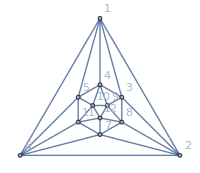
-Graphics-12
{4,24}<->{1<->2,8}
{4,24}<->{1<->3,8}
{4,24}<->{1<->4,8}
{4,24}<->{1<->5,8}
{4,24}<->{1<->6,8}
{4,24}<->{2<->3,8}
{4,24}<->{2<->6,8}
{4,24}<->{2<->7,8}
{4,24}<->{2<->8,8}
{4,24}<->{3<->4,8}
{4,24}<->{3<->8,8}
{4,24}<->{3<->9,8}
{4,24}<->{4<->5,8}
{4,24}<->{4<->9,8}
{4,24}<->{4<->10,8}
{4,24}<->{5<->6,8}
{4,24}<->{5<->10,8}
{4,24}<->{5<->11,8}
{4,24}<->{6<->7,8}
{4,24}<->{6<->11,8}
{4,24}<->{7<->8,8}
{4,24}<->{7<->11,8}
{4,24}<->{7<->12,8}
{4,24}<->{8<->9,8}
{4,24}<->{8<->12,8}
{4,24}<->{9<->10,8}
{4,24}<->{9<->12,8}
{4,24}<->{10<->11,8}
{4,24}<->{10<->12,8}
{4,24}<->{11<->12,8}

```mathematica
With[{g=Graph[plantri [[1]] ]},
Column[{Labeled[Graph[g,VertexLabels->"Name", GraphLayout->"TutteEmbedding",GraphHighlight->CollectMPGEdges[g],GraphHighlightStyle->"Thick", ImageSize->200],Style[VertexCount[g],Red]],
TableForm[Sort[Table[
ExplainContractionCounts[g,e]<->{e,ChromaticPolynomial[EdgeContract[g,e],4]/24},{e,CollectMPGEdges[g]}
]]]}]]
```